## 105A Midterm Fall 2012

Prof. Dubin		              Open book, open notes. 35 points total + 5 point bonus.

Solutions done “by hand” means that I want you to use pen/pencil and paper.
Show all work for full marks.
Internet access is allowed only for connecting to the TED class website.

Answer the following questions that all involve this damped harmonic oscillator ODE:

ⅆ^2/(ⅆ t^2) x(t)+2 ⅆ/ⅆt x(t) +2 x(t) =  f(t).

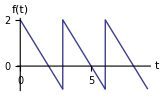
(a)(4 pts)  Plot the direction field in the (x,v) plane (where v=dx/dt ) on -1<x<1, -1<v<1, assuming f(t) = 0. 

(b) (3 pts) Find the general homogeneous solution  for x(t) by hand.

(c) (3 pts) Find a particular solution by hand, assuming f(t) = 2 t.

(d) (5 pts) For  x(0)=-2,x'(0)=-1  and for f(t)=2t, use the result of parts (b) and (c) to obtain the full solution that matches these initial conditions. (If you wish you can use Mathematica to help with solving for the undetermined coefficients; otherwise, do the work by hand. You may only DSolve  to check your answer found with pen and paper.) Plot the solution for x(t) on 0<t<5.

(e) (10 pts) Find the solution for x(t) numerically using the 2nd-order predictor-corrector method, for f(t)=2 t and the initial conditions of part (d). Plot the numerical result for x(t) on 0<t<5, taking a stepsize of 0.1.

(f)(10 pts) For f(t) a  periodic function with period T=3  defined as f(t)=2-t, 0<t<3, (see the plot below) find a particular solution for x(t) using a complex exponential Fourier series representation. (You can use Mathematica to do any required integrals). Plot the particular solution on 0<t<9.

	-Graphics-

(g) (5 pt BONUS) For the boundary conditions x(0)=0 and x(3)=2 , and f(t)=2 t, find and plot a numerical solution for x(t) using the shooting method on 0<t<3. You may use NDSolve in the method; however a single call to NDSolve with boundary conditions x[0]=0, x[3]=2 is not the shooting method, so this is not allowed (except as a check on your work).

### Solution

```mathematica
Clear["Global`*"]
```

#### (a)

The direction field for this system is given by {v,-2v-2x}

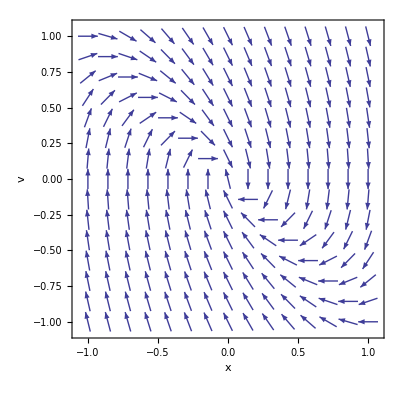

```mathematica
VectorPlot[{v,-2v-2x},{x,-1,1},{v,-1,1},FrameLabel->{"x","v"},VectorScale->{.05,.5,None}]
```

#### (b)

The characteristic polynomial has roots  given by

```mathematica
Solve[s^2 + 2s + 2 == 0,s]
```

{{s→-1-ⅈ},{s→-1+ⅈ}}

So the general homogeneous solution is

```mathematica
xh[t_] = a Exp[-(1+I) t] + b Exp[-(1-I)t];
```

or

```mathematica
xh[t_] =  Exp[- t] (a Cos[t] + b Sin[t])
```

ⅇ^-t (a Cos[t]+b Sin[t])

#### (c)

A particular solution is xp = A+B t. Find A and B by substitution into the ODE: 2B + 2(A+B t) = 2 t , which implies B=1 and A=-1:

```mathematica
xp[t_] = -1+t;
```

Check:

```mathematica
xp''[t]+2 xp'[t] + 2 xp[t]//Expand
```

2 t

#### (d)

The full solution is (taking M=15)

```mathematica
x[t_] = xh[t] + xp[t]
```

-1+t+ⅇ^-t (a Cos[t]+b Sin[t])

Now determine the constants a and b using the initial conditions:

```mathematica
Solve[{x[0]==-2,x'[0]==-1},{a,b}]
```

{{a→-1,b→-3}}

```mathematica
x[t_] = x[t]/.%[[1]]
```

-1+t+ⅇ^-t (-Cos[t]-3 Sin[t])

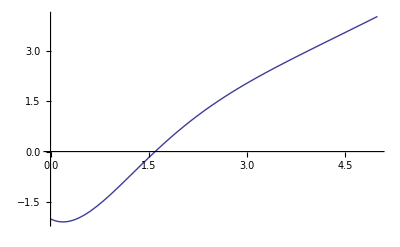

```mathematica
Plot[x[t],{t,0,5},PlotRange->All]
```

#### (e)

Write the 2nd order ODE as 2 coupled first order odes for x(t) and v(t), and define z(t) = (x,v). The differential equations are ⅆx/ⅆt=v, ⅆv/ⅆt = -2x-2v+f(t), or 
				ⅆz/ⅆt ={v, -2x-2v+f(t)}. 
Then the second order-predictor corrector method for z(t) is

```mathematica
Clear[z,z1,F,n];
```

```mathematica
z1[n_] := z[n-1] + Δt F[n-1,z[n-1]];
z[n_] := z[n] = z[n-1] + Δt(F[n,z1[n]] + F[n-1,z[n-1]])/2
```

where

```mathematica
F[n_,{x_,v_}] := {v,-2 v -2 x+ 2n Δt}
```

The initial condition is

```mathematica
z[0] = {-2,-1};
```

We must choose a stepsize:

```mathematica
Δt = 0.1;
```

The solution list is

```mathematica
sol = Table[{n Δt,z[n][[1]]},{n,0,5/Δt + 1}]
```

{{0.,-2},{0.1,-2.07},{0.2,-2.0879},{0.3,-2.06104},{0.4,-1.99625},{0.5,-1.89977},{0.6,-1.77732},{0.7,-1.63403},{0.8,-1.47446},{0.9,-1.30266},{1.,-1.12216},{1.1,-0.935983},{1.2,-0.746733},{1.3,-0.556582},{1.4,-0.367325},{1.5,-0.180415},{1.6,0.00300098},{1.7,0.18205},{1.8,0.356094},{1.9,0.524705},{2.,0.687628},{2.1,0.844759},{2.2,0.996118},{2.3,1.14183},{2.4,1.28208},{2.5,1.41715},{2.6,1.54734},{2.7,1.67299},{2.8,1.79446},{2.9,1.91213},{3.,2.02636},{3.1,2.13753},{3.2,2.24599},{3.3,2.35208},{3.4,2.45611},{3.5,2.5584},{3.6,2.65921},{3.7,2.75881},{3.8,2.85741},{3.9,2.95523},{4.,3.05244},{4.1,3.14922},{4.2,3.24569},{4.3,3.34197},{4.4,3.43817},{4.5,3.53437},{4.6,3.63064},{4.7,3.72704},{4.8,3.8236},{4.9,3.92035},{5.,4.01733},{5.1,4.11455}}

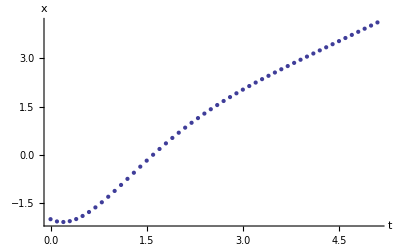

```mathematica
ListPlot[sol,AxesLabel->{"t","x"},PlotRange->All]
```

#### (f)

The particular solution has the form of a Fourier series, x_p(t) = ∑_(n=-∞)^∞ x_n ⅇ^(-ⅈ ω_n t)where ω_n=2π n/T and T=3 is the period of the forcing function. Then
x_n = f_n/(-ω_n^2-2ⅈ ω_n + 2), where f_n is the Fourier coefficient of the forcing function,

```mathematica
Clear["Global`*"]
```

```mathematica
T=3;
ω[n_] = 2 Pi n/T;
f[t_] = 2-t;
```

```mathematica
ff[n_] = Integrate[f[t] Exp[I ω[n] t],{t,0,T}]/T
```

(9+12 ⅈ n π+ⅇ^(2 ⅈ n π) (-9+6 ⅈ n π))/(12 n^2 π^2)

```mathematica
ff[0] = Limit[ff[n],n->0]
```

1/2

check that this is working:

```mathematica
fapprox[t_]=Sum[ff[n] Exp[-I ω[n] t],{n,-10,10}];
```

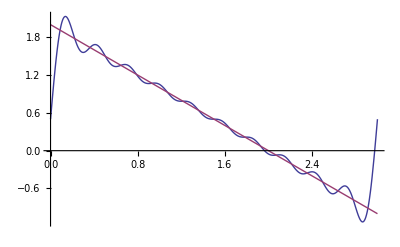

```mathematica
Plot[{fapprox[t],f[t]},{t,0,T}]
```

Create the particular solution as the sum of oscillator responses to each Fourier mode:

```mathematica
xp[t_,M_] := Sum[ff[n] Exp[-I ω[n] t]/(-(ω[n])^2 - 2I ω[n]+ 2),{n,-M,M}];
```

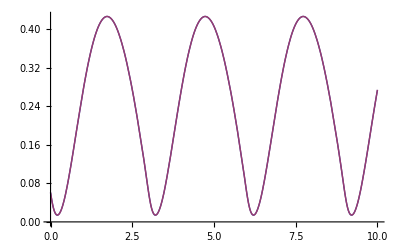

```mathematica
Plot[{xp[t,10],xp[t,15]},{t,0,10}]
```

So M=15 is sufficient to get reasonable accuracy in the result.

#### (g)

```mathematica
Clear["Global`*"]
```

```mathematica
sl[v0_] := NDSolve[{x''[t] + 2x'[t] +2x[t]==2t,x[0]==0,x'[0]==v0},x,{t,0,3}][[1]]
```

```mathematica
xend[v0_] := (x[3]/.sl[v0])/; v0∈Reals
```

```mathematica
xend[-1.]
```

1.94369

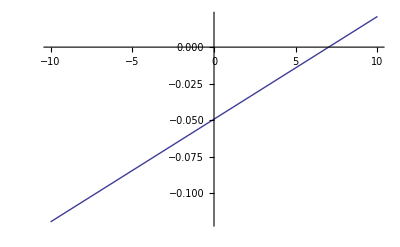

```mathematica
Plot[xend[v0]-2,{v0,-10,10}]
```

```mathematica
FindRoot[xend[v0]==2,{v0,5,7}]
```

{v0→7.01525}

```mathematica
xsol[t_] = x[t]/.sl[v0/.%]
```

InterpolatingFunction[{{0.,3.}},<>][t]

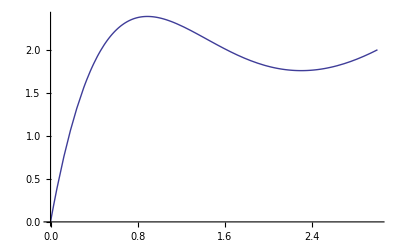

```mathematica
Plot[xsol[t],{t,0,3},PlotRange-> All]
```

Check:

```mathematica
DSolve[{x''[t] + 2x'[t] +2x[t]==2t,x[0]==0,x[3]==2},x[t],t]
```

{{x[t]→ⅇ^-t (-ⅇ^t+ⅇ^t t+Cos[t]-Cot[3] Sin[t])}}

```mathematica
Plot[x[t]/.%[[1]],{t,0,3},PlotRange->All]
```

-Graphics-